```mathematica
(*Capacitante function parameters*)
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
threshold=60;maxtime=1000;plottime=300;
case=4;
Switch[case,
1,C0=1;C1=0.75;T=30;τ2=0.4;τ4=1;,
2,C0=1;C1=0.75;T=50;τ2=0.4;τ4=1;,
3,C0=1;C1=0.85;T=100;τ2=0.4;τ4=1;,
4,C0=1;C1=0.75;T=200;τ2=0.4;τ4=1;
]
point=3;
Switch[point,
1,{τ1,τ3}={0.15,0.7};,
2,{τ1,τ3}={0.15,0.95};,
3,{τ1,τ3}={0.35,0.95};
]

filename=StringJoin["Fig5_case_",ToString[case],"_point_",ToString[point],".png"];
(*HH Parameters from https://www.st-andrews.ac.uk/~wjh/hh_model_intro/, Doesnt seem to be stimulated*)
αm=0.1;
βm=4;
αh=0.07;
βh=1;
αn=0.01;
βn=0.125;
ENa=115;
EK=-12;
EL=10.6;
Voffset =-65;
Vrest=0;
mrest=0.05;
hrest=0.596;
nrest=0.315;
Vαm=25;
Vβm=0;
Vαh=0;
Vβh=30;
Vαn=10;
Vβn=0;
gNa=120;
gK=36;
gL=0.3;
Kαm=10;
Kβm=18;
Kαh=20;
Kβh=10;
Kαn=10;
Kβn=80;
Cm=1;
(*Ionic Chanels*)
Am[V_]=αm (V-Vαm)/(1-Exp[-(V-Vαm)/Kαm]);
Bm[V_]=βm Exp[-(V-Vβm)/Kβm];
Ah[V_]=αh Exp[-(V-Vαh)/Kαh];
Bh[V_]=βh/(1+Exp[-(V-Vβh)/Kβh]);
An[V_]=αn (V-Vαn)/(1-Exp[-(V-Vαn)/Kαn]);
Bn[V_]=βn Exp[-(V-Vβn)/Kβn];
```

```mathematica
(*Solving HH*)

Ct[t_]=Which[Mod[t,T]<τ1 T,C0,Mod[t,T]<τ2 T,C0+(C1-C0)(Mod[t,T]-τ1 T)/((τ2-τ1)T), Mod[t,T]<τ3 T,C1, True,C1+(Mod[t,T] - τ3 T)(C0-C1)/((τ4-τ3)T)];
Ctd[t_]=Which[Mod[t,T]<τ1 T,0,Mod[t,T]<τ2 T,(C1-C0)/((τ2-τ1)T),Mod[t,T]< τ3 T,0, True,(C0-C1)/((τ4-τ3)T)];
(*Solving HH*)
{V,M,H,NN}=NDSolveValue[{Ct[t] v'[t]==-Ctd[t] (v[t]+Voffset)-gNa m[t]^3 h[t](v[t]-ENa)-gK n[t]^4(v[t]-EK) -gL(v[t]-EL),
m'[t]==Am[v[t]](1-m[t])-Bm[v[t]]m[t],
h'[t]==Ah[v[t]](1-h[t])-Bh[v[t]] h[t],
n'[t]==An[v[t]](1-n[t])-Bn[v[t]]n[t],
v[0]==Vrest,m[0]==mrest,h[0]==hrest,n[0]==nrest},
{v,m,h,n},{t,0,maxtime}];
```

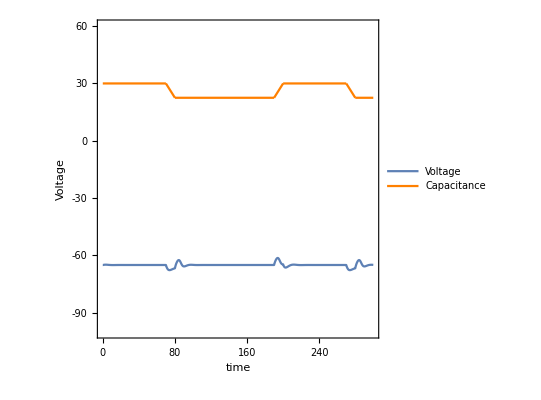

Fig5_case_4_point_3.png

```mathematica
(*Visualization*)
frange={-100,60};
grange={-100/30,60/30};
voltage=Plot[Voffset+V[t],{t,0,plottime},
PlotRange->frange,
TicksStyle->Directive[FontSize->16],
Frame->True,
FrameLabel->{{"Voltage","Capacitance"},{"time",None}},
LabelStyle->Directive[Black,FontSize->16]
];
(*,ColorFunction->Function[{t},Which[Mod[t,2T]<T,Red,True,Default]],ColorFunctionScaling->False];*)(*,PlotLegends->Placed[StringJoin["C0=",ToString[C0],", C1=",ToString[C1],", T= ",ToString[T],",\n","τ1= ",ToString[τ1],", τ2= ",ToString[τ2],", τ3= ",ToString[τ3],",\n","ε=",ToString[ep],", γ=",ToString[γ],", β=",ToString[β]],Above]];*)
capacitance=Plot[{Ct[t]},{t,0,plottime},
PlotPoints->10000,
MaxRecursion->3,
PlotStyle->Orange
];

fticks=FindDivisions[Append[frange,30],10];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
(*gticks=FindDivisions[Append[grange,0.5],10];*)
g1=Legended[
Show[voltage, capacitance/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],
AspectRatio->1,
FrameTicks->{{fticks,gticks},{Automatic,Automatic}}],
Placed[LineLegend[{ColorData[97,"ColorList"][[1]],Orange},
{Style["Voltage",FontSize->18],
Style["Capacitance",FontSize->18]}
,LegendLayout->"Row"],
{{0.5,0.95}}]
]

Export[filename,g1]
```

```mathematica
(*TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/. AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};
frange={-100,60};
grange={-1,1};
fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/. Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]

g2=TwoAxisPlot[{Voffset+V[t],Ct[t]},{t,0,plottime}]*)
```